## 2MBA50 Mathematica Practical Session 2 exercises

This series of notebooks is made in Mathematica 13.3.

Contact: Jan Willem Knopper, MF 5.121, j.w.knopper@tue.nl
Author: ir. W.J.P.M. Kortsmit, small adjustments by Benne de Weger, Jan Willem Knopper.

## Section. Examples and applications

### Name:

### Exercises

#### Exercise Section.Equation

Simplify the following expressions with Mathematica, avoid the use of Simplify and FullSimplify, also study RootReduce:
a) x^2+4 y x+6 z x+4 y^2+9 z^2+12 y z

b) -((3 a-5 c) c^2)/(a b c-a^2 b)+b (((3 a-5 c) c^2)/(a b^2 (c-a))+2/b)-2

c) (√(3492-2016 √3)-32 √3+56)/(8 √3-14)

#### Answer

```mathematica
Factor[x^2+4y*x+6z*x+4y^2+9z^2+12y*z]
Apart[-((3a-5c)c^2)/(a*b*c-a^2*b)+b(((3a-5c)c^2)/(a*b^2(c-a))+2/b)-2]
RootReduce[(Sqrt[3492-2016*Sqrt[3]]-32Sqrt[3]+56)/(8 Sqrt[3]-14)]
```

(x+2 y+3 z)^2

0

-7

#### Exercise Section.Equation

Look up the following concepts by using the help function: Expand, Factor, Coefficient and Exponent. 
Consider the polynomial (x^2-9)^5. 
a) Expand this expression, 
b) determine the degree,
c) determine the coefficient of x^6, and
d) make a list of all coefficients. 
e) decompose the expression in factors 
f) show that this result is equal to the expression.

#### Answer

```mathematica
p = (x^2-9)^5
Expand[p]
Exponent[p,x]
Coefficient[p, x^6]
CoefficientList[p,x]
Factor[p]
CoefficientList[%, x] == CoefficientList[p,x]
```

(-9+x^2)^5

-59049+32805 x^2-7290 x^4+810 x^6-45 x^8+x^10

10

810

{-59049,0,32805,0,-7290,0,810,0,-45,0,1}

(-3+x)^5 (3+x)^5

True

#### Exercise Section.Equation

Use the help function to look up the concept Prime and then make a table of the first hundred prime numbers.

#### Answer

```mathematica
Table[Prime[i], {i,1,100}]
```

{2,3,5,7,11,13,17,19,23,29,31,37,41,43,47,53,59,61,67,71,73,79,83,89,97,101,103,107,109,113,127,131,137,139,149,151,157,163,167,173,179,181,191,193,197,199,211,223,227,229,233,239,241,251,257,263,269,271,277,281,283,293,307,311,313,317,331,337,347,349,353,359,367,373,379,383,389,397,401,409,419,421,431,433,439,443,449,457,461,463,467,479,487,491,499,503,509,521,523,541}

#### Exercise Section.Equation

a) Use the function RandomInteger to make a list of 50 numbers between 1 and 20. Do this directly after evaluating the SeedRandom[“2MBA50”] command, to allow for automatic checking.
Now determine the following this for this list:
        b) the sum of the first and the last element
        c) the difference of the second and the second last element 
        d) the product of the last nineteen elements
NB: Try to be as general as possible. In this exercise: at b), c) and d) try to come up with a  generalized Mathematica-command that can be used unchanged for each list of an arbitrary number of arbitrary numbers of arbitrary size. Hint: You can define a function like f[l_]:=.... Make sure to use a more descriptive name!

#### Answer

```mathematica
SeedRandom["2MBA50"]
Table[RandomInteger[{1,20}],50]
```

RandomGeneratorState[…]

{1,16,17,18,18,9,11,5,19,8,15,12,8,9,12,20,8,16,11,8,19,14,14,8,20,8,2,19,6,4,11,6,3,16,2,9,12,11,12,4,1,15,20,6,18,4,15,13,10,10}

#### Exercise Section.Equation

a) Make a table of the numbers √n for n=0 up to and including 20, each of the numbers in 8 decimals.
b) Give the numerical value of π and sin(3) in 10 decimals.
c) Compute ∑_(k=1)^n k^s for s=7,8 and 9.
d) Compute the numerical value of ∑_(n=1)^∞ 1/n^3 in four decimals.

#### Answer

```mathematica
Table[N[Sqrt[n],9], {n,0,20}]
N[Pi,11]
N[Sin[3], 10]
Table[Sum[k^s,{k, n}], {s,7,9}, {n,1,20}]
N[Sum[1/n^3,{n,1,Infinity}],5]
```

{0,1.,1.41421356,1.73205081,2.,2.23606798,2.44948974,2.64575131,2.82842712,3.,3.16227766,3.31662479,3.46410162,3.60555128,3.74165739,3.87298335,4.,4.12310563,4.24264069,4.35889894,4.47213595}

3.1415926536

0.1411200081

{{1,129,2316,18700,96825,376761,1200304,3297456,8080425,18080425,37567596,73399404,136147921,241561425,412420800,680856256,1091194929,1703414961,2597286700,3877286700},{1,257,6818,72354,462979,2142595,7907396,24684612,67731333,167731333,382090214,812071910,1627802631,3103591687,5666482312,9961449608,16937207049,27957167625,44940730666,70540730666},{1,513,20196,282340,2235465,12313161,52666768,186884496,574304985,1574304985,3932252676,9092033028,19696532401,40357579185,78800938560,147520415296,266108291793,464467582161,787155279940,1299155279940}}

1.2021

#### Exercise Section.Equation

a) Solve: x^4-5 x^2-3=0 and write, by using Mathematica, the solutions in a list.
b) Solve the following system of equations: x^2+y^2=1, x+3 y=0.
c) Use the function ContourPlot to give a graphical representation of the equations in b).

#### Answer

{{x→-ⅈ √(1/2 (-5+√37))},{x→ⅈ √(1/2 (-5+√37))},{x→-√(1/2 (5+√37))},{x→√(1/2 (5+√37))}}

{{x→-3/(√10),y→1/(√10)},{x→3/(√10),y→-1/(√10)}}

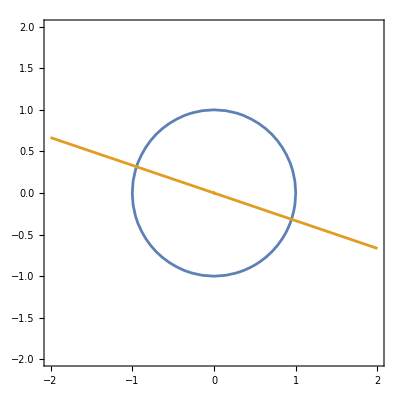

```mathematica
Solve[x^4-5x^2 - 3 == 0]

Solve[x^2 + y^2 == 1 && x + 3y ==0 , {x,y}]

ContourPlot[{x^2+y^2==1, x+3y == 0},{x,-2,2}, {y,-2,2}]
```

#### Exercise Section.Equation

The instruction Solve cannot solve the following equation: x^6-9 x^4-4 x^3+27 x^2-36 x-23==0. 
a) Show, by using Mathematica, that 2^(1/3)+√3 is a solution 
b) find numerical approximations for the other solutions. Put these solutions in a list. 
c) Which solution corresponds to the given solution?

#### Answer

```mathematica
Together[x^6-9 x^4-4 x^3+27 x^2-36 x-23  /. x->2^(1/3)+3^(1/2)]
Solve[x^6-9 x^4-4 x^3+27 x^2-36 x-23==0]
%[[2]]
```

0

{{x→Root-0.472Root[-23-36 #1+27 #1^2-4 #1^3-9 #1^4+#1^6&,1]-0.4721297576740041},{x→Root2.99Root[-23-36 #1+27 #1^2-4 #1^3-9 #1^4+#1^6&,2]2.9919718574637506},{x→Root-2.36-1.09 ⅈRoot[-23-36 #1+27 #1^2-4 #1^3-9 #1^4+#1^6&,3]-2.362011332516314},{x→Root-2.36+1.09 ⅈRoot[-23-36 #1+27 #1^2-4 #1^3-9 #1^4+#1^6&,4]-2.362011332516314},{x→Root1.10-1.09 ⅈRoot[-23-36 #1+27 #1^2-4 #1^3-9 #1^4+#1^6&,5]1.1020902826214407},{x→Root1.10+1.09 ⅈRoot[-23-36 #1+27 #1^2-4 #1^3-9 #1^4+#1^6&,6]1.1020902826214407}}

{x→Root2.99Root[-23-36 #1+27 #1^2-4 #1^3-9 #1^4+#1^6&,2]2.9919718574637506}

#### Exercise Section.Equation

Consider the system of equations:  {3 x+2 y-2 z==3
2 x-3 y+3 z==7
a) Solve x and z as functions of y. 
b) Which solution do we find for y=3?

#### Answer

```mathematica
Solve[3x+2y-2z==3 && 2x-3y+3z == 7, {x,z}]
% /. y -> 3
```

{{x→23/13,z→1/13 (15+13 y)}}

{{x→23/13,z→54/13}}